# OEIS Package: Benchmark

Real, captured timings from a single run of Benchmarks/Benchmark.wls -- not illustrative. Network-bound operations depend on the OEIS server and connection, so treat absolute numbers as indicative; the relative shape (pure/local-formula operations are essentially free; network calls dominate) is the useful takeaway.

$Version: 11.2.0 for Linux x86 (64-bit) (September 11, 2017)

## Results

Operation | Time (s)
OEISValidateIDQ (pure) | 0.
OEISURL, bFile->True (pure) | 0.0001
OEISImport, "Description" (network) | 0.7112
OEISImport, "Data" (network) | 0.4618
OEISImport, "MinData" (network) | 0.3757
OEISFunction (network) | 1.0187
OEISbFile local formula, VMax=100 | 0.1496
OEISbFile local formula, VMax=1000 | 0.1563
OEISbFile local formula, VMax=5000 | 0.2081
OEISbFile local formula, VMax=20000 | 0.4187
OEISbFile OEIS-data fallback, VMax=1000 | 1.682

## Chart

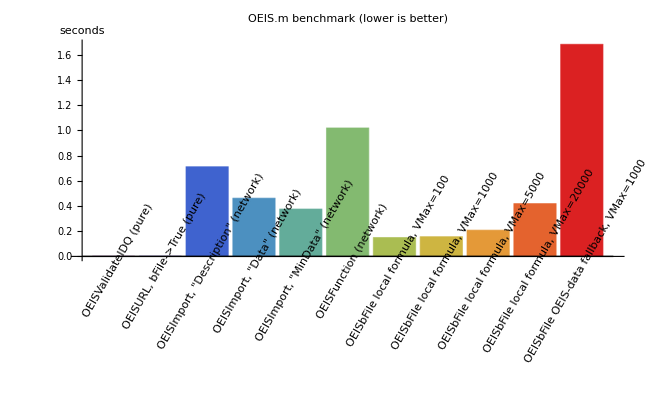

## Reading the OEISbFile rows

The four "local formula" rows use a session-defined A358061[n_] (see the OEISbFile reference page and the tutorial) with VMax growing from 100 to 20000: since OEISbFile only makes one network call (to look up the sequence's starting offset) regardless of VMax, their timings mostly reflect pure local computation and scale far more gently than a network round trip per term would. The "OEIS-data fallback" row -- no local definition -- pays for two network calls (the offset lookup, then OEISFunction's own description/data fetch) and is capped by how many terms OEIS has actually published.